## vdP

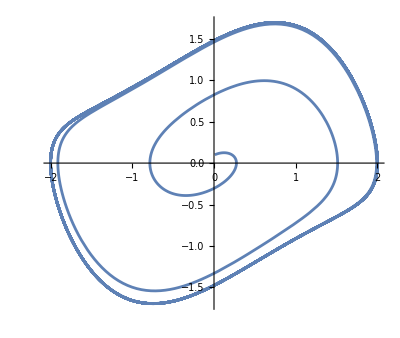

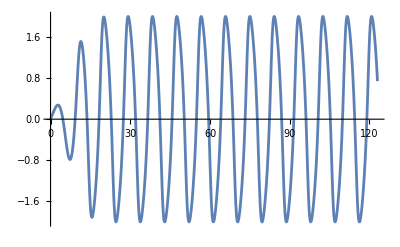

```mathematica
TMax=123;
μ=1;
xSol=NDSolveValue[
{
2 x''[t]-μ(1-x[t]^2)x'[t]+x[t]==0,
x[0]==0.01,
x'[0]==0.1},
x,
{t,0,TMax}
];
ParametricPlot[{xSol[t],xSol'[t]},{t,0, TMax}]
Plot[xSol[t],{t,0,TMax}]
```

```mathematica
■^(⏞^□)
```

## Rosseler One

## Rosseler Two`

{0.22,0.2,234}

-Graphics3D-

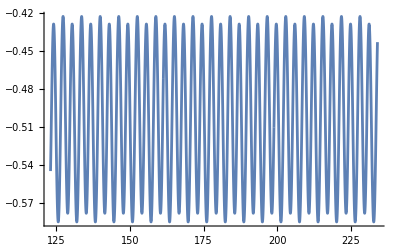

```mathematica
{a,b,TMax}={0.22,0.2,234}
{xSol,ySol,zSol}=NDSolveValue[{
x'[t]==-y[t]-z[t],
y'[t]==x[t],
z'[t]==a (y[t]-y[t]^2)- b z[t],
x[0]==0.01,
y[0]==0.02,
z[0]==0.03
},
{x,y,z},{t, 0, TMax}];
ParametricPlot3D[{xSol[t],ySol[t],zSol[t]},
{t, 123, TMax},PlotPoints->10^4]
Plot[zSol[t],
{t, 123, TMax},PlotPoints->10^4]
```